```mathematica
LbCount=0;
LwCount=0;
A={{1,0},{0,1}};
For[i=0,i≤15,i++,If[EvenQ[i],A=A.(Inverse[{{Exp[I(LwCount*Lw+LbCount*Lb)*kf],Exp[-I(LwCount*Lw+LbCount*Lb)*kf]},{kf*Exp[I*(LwCount*Lw+LbCount*Lb)*kf],-kf*Exp[-I*(LwCount*Lw+LbCount*Lb)*kf]}}].{{Exp[I(LwCount*Lw+LbCount*Lb)*kp],Exp[-I(LwCount*Lw+LbCount*Lb)*kp]},{kp*Exp[I*(LwCount*Lw+LbCount*Lb)*kp],-kp*Exp[-I*(LwCount*Lw+LbCount*Lb)*kp]}}),A=A.(Inverse[{{Exp[I(LwCount*Lw+LbCount*Lb)*kp],Exp[-I(LwCount*Lw+LbCount*Lb)*kp]},{kp*Exp[I*(LwCount*Lw+LbCount*Lb)*kp],-kp*Exp[-I*(LwCount*Lw+LbCount*Lb)*kp]}}].{{Exp[I(LwCount*Lw+LbCount*Lb)*kf],Exp[-I(LwCount*Lw+LbCount*Lb)*kf]},{kf*Exp[I*(LwCount*Lw+LbCount*Lb)*kf],-kf*Exp[-I*(LwCount*Lw+LbCount*Lb)*kf]}})];If[EvenQ[i],LbCount=LbCount+1,LwCount=LwCount+1];]
```

```mathematica
m=511*10^3/(2.998*10^8)^2; (* mass of an electron in keV/c^2 *)
V=10; (* Potential energy in eV *)
hb=6.582*10^-16; (* hbar in eV*s *)
kp=Sqrt[2*m*(E0-V)/hb^2];
kf=Sqrt[2*m*E0/hb^2];
Lw=.4*10^-9 ; (* Well width in nm *)
Lb=.1*10^-9;(* Barrier width in nm *)
p11=A[[1]][[1]];
```

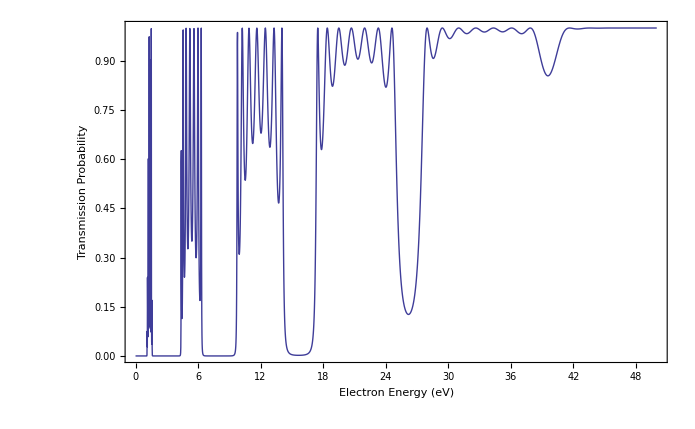

```mathematica
Plot[1/(p11*Conjugate[p11]),{E0,0,50},Frame-> True,FrameLabel->{{"Transmission Probability",""},{"Electron Energy (eV)","Transmission Probablity vs. Electron Energy"}},LabelStyle->Directive[Large]]
```

```mathematica
(*Plot[{Re[p11],Piecewise[{{Re[p11],-1≤Re[p11]≤1}},_]},{E0,0,30},Filling-> {2->{Axis,Yellow}},PlotStyle->{Green,Directive[Red,Thick,Style->Large]},Frame->True,FrameLabel->{{"Re[p11] ",""},{"Electron energy (eV)","Re[p11] vs. Electron Energy"}},RotateLabel->True,LabelStyle->Large]*)
```